```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True];
<<Wolfram`QuantumFramework`
```

Qiskit should be installed:

```mathematica
ResourceFunction["PythonPackageInformation"]["qiskit"]["Version"]
```

0.36.1

Test circuit conversion:

```mathematica
circuit=QuantumCircuitOperator["Toffoli"]
```

QuantumCircuitOperator[…]

```mathematica
qiskitCircuit=circuit["Qiskit"]
```

QiskitCircuit[…]

```mathematica
circuit[QuantumState["110"]]["Formula"]
```

ⅈ ⅇ^((ⅈ π)/4) (-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)) 111

```mathematica
qiskitCircuit[QuantumState["110"]]["Formula"]
```

1. 111

```mathematica
qiskitCircuit["Graphics","Scale"->1]
```

-Graphics-

Compilation into a QuantumOperator:

```mathematica
qiskitCircuit["QuantumOperator"]
```

QuantumOperator[…]

```mathematica
circuit["CircuitOperator"]
```

QuantumOperator[…]

```mathematica
%==%%
```

True

Acting on a state:

```mathematica
qiskitCircuit[QuantumState["010"]]
```

QuantumState[…]

```mathematica
circuit[QuantumState["010"]]
```

QuantumState[…]

```mathematica
%==%%
```

True

Adding measurement:

```mathematica
circuitM=QuantumMeasurementOperator[{1,3}]@circuit
```

QuantumCircuitOperator[…]

```mathematica
qiskitCircuitM=circuitM["Qiskit"]
```

QiskitCircuit[…]

Target qubits are reset:

```mathematica
qiskitCircuitM[QuantumState["010"]]
```

QuantumMeasurement[…]

```mathematica
circuitM[QuantumState["010"]]
```

QuantumMeasurement[…]

```mathematica
%["Probabilities"]==%%["Probabilities"]
```

True

#### Grover Algorithm

```mathematica
Remove["Global`Quantum*"]
```

```mathematica
grover=QuantumMeasurementOperator[Range[3]]@QuantumCircuitOperator[{"Grover",a&&!b&&c}]
```

QuantumCircuitOperator[…]

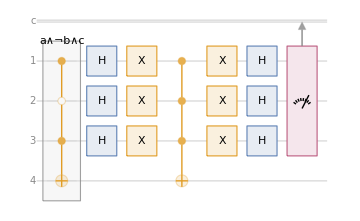

```mathematica
grover["Diagram"]
```

Decomposition of MCX is required for it to work:

```mathematica
grover["Qiskit"]
```

QiskitCircuit[…]

```mathematica
groverQiskit=grover[[;;]]["Qiskit"]["Decompose"]
```

QiskitCircuit[…]

```mathematica
groverQiskit[initState]
```

QuantumState[…]

```mathematica
grover["Qiskit"]["Diagram"]
```

-Graphics-

```mathematica
initState=QuantumOperator["Z",{4}]@QuantumState[{"UniformSuperposition",4}];
```

```mathematica
exactMeasurement=grover[initState]
```

QuantumMeasurement[…]

```mathematica
simMeasurement=groverQiskit[initState]
```

QuantumMeasurement[…]

Use IBMQ simulator:

```mathematica
grover[[;;-2]]["Qiskit"]
```

QiskitCircuit[…]

```mathematica
grover[[;;-2]][initState]
```

QuantumState[…]

```mathematica
grover[[;;-2]]["Qiskit"][initState,"Provider"->"IBMQ"]
```

ibmqfactory.load_account:WARNING:2022-07-09 00:15:30,229: Credentials are already in use. The existing account in the session will be replaced.

```mathematica
cloudSimMeasurement=groverQiskit[initState,"Provider"->"IBMQ"]
```

ibmqfactory.load_account:WARNING:2022-07-08 22:43:39,279: Credentials are already in use. The existing account in the session will be replaced.

QuantumMeasurement[…]

This took ~30 minutes (it’s not asynchronous):

```mathematica
deviceMeasurement=groverQiskit[initState,"Provider"->"IBMQ","Backend"->"ibmq_lima"]
```

ibmqfactory.load_account:WARNING:2023-02-16 20:35:35,945: Credentials are already in use. The existing account in the session will be replaced.

QuantumMeasurement[…]

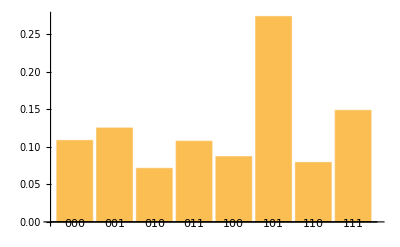

```mathematica
BarChart[deviceMeasurement["Probabilities"],ChartLabels->Automatic]
```

```mathematica
QuantumCircuitOperator@QuantumLabelName@QuantumCircuitOperator[QuantumState[{"RandomPure",3}]]
```

QuantumCircuitOperator[…]

```mathematica
qiskit=QuantumCircuitOperator[Join[QuantumLabelName@QuantumCircuitOperator[QuantumState[{"RandomPure",3}]],{{1,2,3}}]]["Qiskit"]
```

QiskitCircuit[…]

```mathematica
qiskit["Diagram"]
```

-Graphics-

```mathematica
qiskit["Provider"->"IBMQ","Backend"->"ibmq_lima"]
```

ibmqfactory.load_account:WARNING:2023-02-16 20:55:29,945: Credentials are already in use. The existing account in the session will be replaced.

QuantumMeasurement[…]

```mathematica
qiskit["Provider"->{"IBMQ","Token"->token}(*,"Backend"->"ibmq_lima"*)]
```

ibmqfactory.load_account:WARNING:2023-02-16 21:19:48,386: Credentials are already in use. The existing account in the session will be replaced.

QuantumMeasurement[…]

```mathematica
qiskit["Provider"->{"IBMQ","Token"->token},"Backend"->"ibmq_lima"]
```

ibmqfactory.load_account:WARNING:2023-02-16 21:20:40,433: Credentials are already in use. The existing account in the session will be replaced.

QuantumMeasurement[…]

```mathematica
ResourceFunction["PythonPackageInstall"][QF`PackageScope`$PythonSession,"qiskit-ibm-runtime"]
```

Success[…]

```mathematica
ExternalEvaluate[QF`PackageScope`$PythonSession,"
from qiskit import IBMQ
dir(IBMQ)
"]
```

{__bool__,__class__,__delattr__,__dict__,__dir__,__doc__,__eq__,__format__,__ge__,__getattr__,__getattribute__,__gt__,__hash__,__init__,__init_subclass__,__le__,__lt__,__module__,__ne__,__new__,__reduce__,__reduce_ex__,__repr__,__setattr__,__sizeof__,__str__,__subclasshook__,__weakref__,ibmq}

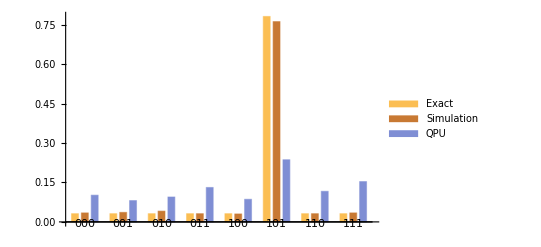

```mathematica
BarChart[Merge[{exactMeasurement["Probabilities"],simMeasurement["Probabilities"],deviceMeasurement["Probabilities"]},Identity],ChartLabels->Automatic,
ChartLegends->Placed[{"Exact","Simulation","QPU"},Below]]
```